```mathematica
ClearAll["Global'*"]
```

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

```mathematica
(* list fonts*)
fontlist=FE`Evaluate[FEPrivate`GetPopupList["MenuListFonts"]];
```

## What is this Notebook?

This notebook produces Figure 3 of the main text, in which height and pressure profiles are plotted as a function of elastic Leidenfrost number. 

The corresponding raw COMSOL dataset is named “06-2022-MykytkaIndrajitData” 

The code reads in the raw data, applies the rescalings derived in the SM of the manuscript, and plots the resulting rescaled height and pressure fields as λ varies. 

The last section “3D visualisation of the Data” outputs some 3D versions of height profiles, for visualisation purposes alone. These 3D plots are used in Figure 2 of the main text.

## Rescaled Height and Pressure Profiles in the Contact and Neck Regions

```mathematica
(*GLOBAL SWITCH --- ARE WE EXPORTING STUFF?*)
print=0;
```

```mathematica
(* In this dataset, we can through R, fixing all else*)
(* The Material parameters*)

η=2 10^-5;
κ=3 10^-2;
L=2.6 10^6;
ΔT=215-100;
ρ=5 10^-1;
Subscript[ρ, l]=10^3;
(* elastic constants*)
e=50 10^3;
ν=1/2;
g=9.81;
d=3/4((1-ν^2)/e);
(* derived quantities*)
Π0=(κ ΔT η)/(L ρ);
```

```mathematica
(* Functions for non-dimensionalising, as R varies*)
F[R_]:=4/3 π Subscript[ρ, l] g R^3;
Rh[R_]:=(F[R]d R)^(1/3)
deltah[R_]:=Rh[R]^2/R;
Ph[R_]:=3/(2π)F[R]/Rh[R]^2;
lambda[R_]:=(2π)/3 Π0 F[R]^(-7/3)R^(8/3)d^(-4/3)
```

```mathematica
(* watch out for the units in the data here!!!*)
(* I'll convert everything to SI*)
dir=ParentDirectory[NotebookDirectory[]]<>"/06-2022-MykytkaIndrajitData/"
names={
"Data-Pressure-R0.1905mm-E50000Palambda102-extrafinemeshnew-Indrajitszie.txt"
,"Data-Pressure-R0.3240mm-E50000Palambda101-extrafinemesh-Indrajitsize.txt"
,"Data-Pressure-R0.5512mm-E50000Palambda10-0-extrafinemesh-Indrajit-size.txt"
,"Data-Pressure-R0.938mm-E50000Palambda10-1-extrafinemesh-Indrajit-size.txt"
,"Data-Pressure-R1.595mm-E50000Palambda10-2-extrafinefine-Indrajit-Sze.txt"
,"Data-Pressure-R2.714mm-E50000Palambda10-3-extrafinemesh-Indrajit-sizeexp.txt"
,"Data-Pressure-R4.617mm-E50000Palambda10-4-extrafine-Indrajit-szieexp.txt"
,"Data-Pressure-R7.855mm-E50000Palambda10-5-extremelyfinenew-Indrajit-Sze.txt"
,"profile+pressure-R13.364mm-E50000Palambda10-6-extrafinemesh.txt"
,"Pressure-R22.736mm-E50000Pa_lambda10-7extra.txt"
,"profile+pressure_R38.7mm_E50000.txt"};
Rs={0.1905,0.324,0.5512,0.938,1.595,2.714,4.617,7.855,13.364,22.736,38.7} 10^-3;
(* sanity check - do the lambdas come out right?*)
lambdasFromRs=Map[lambda,Rs];
lambdas={10^2,10^1,10^0,10^-1,10^-2,10^-3,10^-4,10^-5,10^-6,10^-7,10^-8};
lambdasFromRs/lambdas (* should all be about 1*)
```

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/06-2022-MykytkaIndrajitData/

{0.99873,0.999919,0.999969,0.998729,1.00084,1.00004,1.00023,1.00006,0.999851,0.999767,0.997499}

```mathematica
(* DATA EXTRACTION*)
data={};
IndrajitHeights={};
IndrajitHeightsUnrescaled={};
IndrajitPressures={};
For[i=1,i<=Length[names],i++,
path=dir<>names[[i]];
tempdata= Import[path,"Table"];

(* extract the height and pressure profiles*)
(* I'm going to take everything to SI*)

tempr=tempdata[[;;,1]] 10^-3;
tempHeight=tempdata[[;;,2]] 10^-3;
tempPressure=tempdata[[;;,3]];

(* first, store the unrescaled height values*)
temprtempHeightUnrescaled=MapThread[{#1,#2}&,{tempr/Rh[Rs[[i]]],tempHeight}];

(* As is stands, everything is dimensional. Lets rescale by the Hertzian values*)
tempR=Rs[[i]];
tempr=tempr/Rh[tempR];
tempHeight=tempHeight/deltah[tempR];
tempPressure=tempPressure/Ph[tempR];

(* construct interpolating functions for the height and the pressure*)
temprtempHeight=MapThread[{#1,#2}&,{tempr,tempHeight}];
temprtempPressure=MapThread[{#1,#2}&,{tempr,tempPressure}];

heightunrescaled=Interpolation[temprtempHeightUnrescaled];
height=Interpolation[temprtempHeight];
pressure=Interpolation[temprtempPressure];

(* append them to a list*)
AppendTo[IndrajitHeightsUnrescaled,heightunrescaled];
AppendTo[IndrajitHeights,height];
AppendTo[IndrajitPressures,pressure];
]
```

### Pressure Plot

```mathematica
(* colorschemes*)
(* colourscheme, import the mpl schemes*)
(*https://mathematica.stackexchange.com/questions/127306/colormaps-for-linear-visual-perception-and-grayscale-printing*)
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
MyColorFunc=MPLColorMap["Plasma"];
MyColorFunc2=MPLColorMap["Viridis"];
(* pt to cm conversion*)
cm = 72/2.54;
```

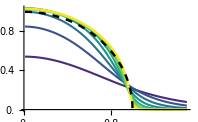

```mathematica
(* styling for the ticks and axes*)
tickfontsize=6;
ticklen={0,-0.02};
xticks=Table[{i,i,ticklen},{i,0,1.5,0.2}];
yticks=Table[{i,i,ticklen},{i,0,1,0.2}];
myticks={xticks,yticks};
tickthickness=0.3;
axesthickness=0.4;

(* plot the data*)
innercut=0.01;
outercut=1.5;
idx={4,5,6,7,8,9,10,11};
n=Length[lambdas[[idx]]];
linethickness=1.5;(* line thickness*)

mycolormap=Map[#1->MyColorFunc2[Position[idx,#1][[1]][[1]]/Length[idx]]&,idx];
myplotstyle=Map[{AbsoluteThickness[linethickness],#1/.mycolormap}&,idx];
(* actually plot it*)
temp=MapThread[#1[r]&,{IndrajitPressures,lambdas}][[idx]];
p1=Plot[{temp},{r,innercut,outercut}
,PlotRange->All
(*,PlotLegends->legend*)(* no legends atm*)
,PlotStyle->myplotstyle];

(* Hertzian Limit*)
PHertz[r_]:=Sqrt[1-r^2]
p2=Plot[PHertz[r],{r,innercut,outercut}
,PlotStyle->{AbsoluteThickness[1.15*linethickness],Black,Dashed}];

(* the combined graphic*)
mygraphic=Show[p1,p2
,Ticks->myticks
,TicksStyle->Directive[Black,AbsoluteThickness[tickthickness],Directive[FontSize->tickfontsize]]
,AxesStyle->Directive[Black,AbsoluteThickness[axesthickness]]
,ImageSize->7cm
,BaseStyle->{FontFamily->"Source Sans Pro",FontSize->8}
]
```

```mathematica
If[1==print
,Export[NotebookDirectory[]<>"IndrajitsData-PressureProfilesUnrescaled.pdf",mygraphic]
]
```

### Collapse in the Neck Region

```mathematica
idx={6,7,8,9,10,11};
λp=3/32;
λd=3/16;

(*plot range*)
innercut=-3;
outercut=3;

(* styling for the ticks and axes*)
tickfontsize=6;
ticklen={0,-0.02};

xticks=Table[{i,i,ticklen},{i,0-3,3,1}];
yticks=Table[{i,i,ticklen},{i,0,2,1}];
myticks={xticks,yticks};
tickthickness=0.3;
axesthickness=0.4;

(* plot the data*)
linethickness=1.5;(* line thickness*)
(* for the colors, subset the overall list of colors by the indices we want to plot*)
myplotstyle=Map[{AbsoluteThickness[linethickness],#1/.mycolormap}&,idx]
(*myplotstyle=Map[{AbsoluteThickness[linethickness],MyColorFunc2[#1/n]}&,Table[i,{i,1,n}]];*)
(* actually plot it*)
temp=MapThread[(#1[((#2)^λd η2)+1])/(#2)^λp&,{IndrajitPressures,lambdas}][[idx]];
mygraphic=Plot[{temp},{η2,innercut,outercut}
,PlotStyle->myplotstyle
(*,PlotLegends->legend*)(* no legends atm*)
,Ticks->myticks
,TicksStyle->Directive[Black,AbsoluteThickness[tickthickness],Directive[FontSize->tickfontsize]]
,AxesStyle->Directive[Black,AbsoluteThickness[axesthickness]]
,ImageSize-> 3.0cm
,BaseStyle->{FontFamily->"Source Sans Pro",FontSize->8}
]
If[1==print,
Export[NotebookDirectory[]<>"IndrajitsData-PressureProfilesRescaledNeckRegion.pdf",mygraphic]
]
```

{{AbsoluteThickness[1.5],RGBColor[0.17330183625, 0.4473856625, 0.5578503850000001]},{AbsoluteThickness[1.5],RGBColor[0.128148545, 0.56510697, 0.55089239]},{AbsoluteThickness[1.5],RGBColor[0.15537807875, 0.6815391125, 0.50323975875]},{AbsoluteThickness[1.5],RGBColor[0.36285894750000003, 0.7866951249999999, 0.3865887425]},{AbsoluteThickness[1.5],RGBColor[0.6693580637500001, 0.86221716875, 0.19544434375]},{AbsoluteThickness[1.5],RGBColor[0.99324789, 0.90615657, 0.1439362]}}

-Graphics-

### Height Plot

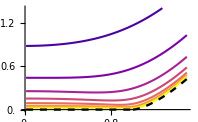

```mathematica
(* styling for the ticks and axes*)
tickfontsize=6;
ticklen={0,-0.02};

xticks=Table[{i,i,ticklen},{i,0,1.5,0.2}];
yticks=Table[{i,i,ticklen},{i,0,1.2,0.2}];
myticks={xticks,yticks};
tickthickness=0.3;
axesthickness=0.4;
linethickness=1.5;(* line thickness*)

(* plot the data*)
(*plot range*)
innercut=0.01;
outercut=1.5;
idx={4,5,6,7,8,9,10,11};
n=Length[lambdas[[idx]]];
mycolormap=Map[#1->MyColorFunc[Position[idx,#1][[1]][[1]]/Length[idx]]&,idx];
myplotstyle=Map[{AbsoluteThickness[linethickness],#1/.mycolormap}&,idx];

(* actually plot it*)
temp=MapThread[#1[r]&,{IndrajitHeights,lambdas}][[idx]];
p1=Plot[{temp},{r,innercut,outercut}
(*,PlotRange->All*)
,PlotRange->{{0,1.4}{0,1}}
(*,PlotLegends->legend*)(* no legends atm*)
,PlotStyle->myplotstyle];

(* Hertzian Limit*)
hHertz[r_]:=Piecewise[{{-1+(r+1)^2/2+1/π((2-(r+1)^2)ArcSin[1/(r+1)]+(r+1)(1-(1/(r+1))^2)^(1/2)),r>0}},0]
p2=Plot[hHertz[r-1],{r,innercut,outercut}
,PlotStyle->{AbsoluteThickness[1.1*linethickness],Black,Dashed}
,PlotRange->{{0,1.4}{0,1}}
(*,PlotRange->All*)];

(* the combined graphic*)
mygraphic=Show[p1,p2
,Ticks->myticks
,TicksStyle->Directive[Black,AbsoluteThickness[tickthickness],Directive[FontSize->tickfontsize]]
,AxesStyle->Directive[Black,AbsoluteThickness[axesthickness]]
,ImageSize-> 7 cm
,BaseStyle->{FontFamily->"Source Sans Pro",FontSize->8}
]
If[1==print,
Export[NotebookDirectory[]<>"IndrajitsData-HeightProfilesUnrescaled.pdf",mygraphic]
]
```

### Height Collapse in Central Region

```mathematica
(*plot range*)
innercut=0.01;
outercut=1.2;

(* styling for the ticks and axes*)
tickfontsize=6;
ticklen={0,-0.02};

xticks=Table[{i,i,ticklen},{i,0,1,0.5}];
yticks=Table[{i,i,ticklen},{i,0,2,0.5}];
myticks={xticks,yticks};
tickthickness=0.3;
axesthickness=0.4;

(* plot the data*)
idx={5,6,7,8,9,10,11};
(* plot the data*)
linethickness=1.5;(* line thickness*)
(* for the colors, subset the overall list of colors by the indices we want to plot*)
myplotstyle=Map[{AbsoluteThickness[linethickness],#1/.mycolormap}&,idx];


(* actually plot it*)
temp=MapThread[(#2^(-1/4))(#1[(r)])&,{IndrajitHeights,lambdas}][[idx]];
mygraphic=Plot[{temp},{r,innercut,outercut}
,PlotStyle->myplotstyle
(*,PlotLegends->legend*)(* no legends atm*)
,Ticks->myticks
,TicksStyle->Directive[Black,AbsoluteThickness[tickthickness],Directive[FontSize->tickfontsize]]
,AxesStyle->Directive[Black,AbsoluteThickness[axesthickness]]
,ImageSize-> 3.2 cm
,BaseStyle->{FontFamily->"Source Sans Pro",FontSize->8}
]

If[1==print,
Export[NotebookDirectory[]<>"IndrajitsData-HeightProfilesRescaledCentralRegion.pdf",mygraphic]
]
```

-Graphics-

### Height Collapse in Neck Region

```mathematica
λh=9/32;
λd=3/16;
idx={6,7,8,9,10,11};
(*plot range*)
innercut=-3;
outercut=1;

(* styling for the ticks and axes*)
tickfontsize=6;
ticklen={0,-0.02};

xticks=Table[{i,i,ticklen},{i,-3,1,1}];
yticks=Table[{i,i,ticklen},{i,0,3,1}];
myticks={xticks,yticks};
tickthickness=0.3;
axesthickness=0.4;

(* plot the data*)
linethickness=1.5;(* line thickness*)
(* for the colors, subset the overall list of colors by the indices we want to plot*)
myplotstyle=Map[{AbsoluteThickness[linethickness],#1/.mycolormap}&,idx];
(* actually plot it*)
temp=MapThread[(#1[((#2)^λd η2)+1])/(#2)^λh&,{IndrajitHeights,lambdas}][[idx]];
mygraphic=Plot[{temp},{η2,innercut,outercut}
,PlotStyle->myplotstyle
(*,PlotLegends->legend*)(* no legends atm*)
,Ticks->myticks
,TicksStyle->Directive[Black,AbsoluteThickness[tickthickness],Directive[FontSize->tickfontsize]]
,AxesStyle->Directive[Black,AbsoluteThickness[axesthickness]]
,ImageSize-> 2.6 cm
,BaseStyle->{FontFamily->"Source Sans Pro",FontSize->8}
]
if[1==print,
Export[NotebookDirectory[]<>"IndrajitsData-HeightProfilesRescaledNeckRegion.pdf",mygraphic]
]
```

-Graphics-

## 3D visualisation of the Data

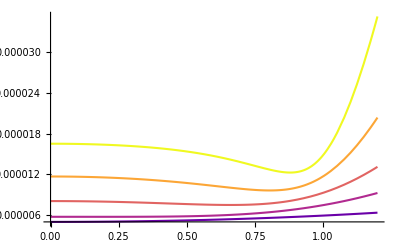

```mathematica
(* styling for the ticks and axes*)
tickfontsize=6;
ticklen={0,-0.02};

xticks=Table[{i,i,ticklen},{i,0,1.5,0.2}];
yticks=Table[{i,i,ticklen},{i,0,1.2,0.2}];
myticks={xticks,yticks};
tickthickness=0.3;
axesthickness=0.4;
linethickness=1.5;(* line thickness*)

(* plot the data*)
(*plot range*)
innercut=0.000;
outercut=1.2;
idx={3,5,6,7,8};
n=Length[lambdas[[idx]]];
myplotstyle=Map[{AbsoluteThickness[linethickness],MyColorFunc[#1/n]}&,Table[i,{i,1,n}]];
(* actually plot it*)
temp=MapThread[#1[r]&,{IndrajitHeightsUnrescaled,lambdas}][[idx]];
p1=Plot[{temp},{r,innercut,outercut}
,PlotRange->All
(*,PlotLegends->legend*)(* no legends atm*)
,PlotStyle->myplotstyle]
```

```mathematica
rmax=1.05;
vscale=1;
opac=0.9;
p1=RevolutionPlot3D[vscale temp[[5]],{r,0,rmax},{θ,0,π},MaxRecursion->10,MeshStyle->None,PlotRange->All
,PlotStyle->{Directive[MyColorFunc[5/n],Specularity[White,10]],Opacity[opac]}
];

Export[NotebookDirectory[]<>"p1.obj", p1]

gInidicatrix =ParametricPlot3D[{r,0,vscale temp[[5]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];
gInidicatrix2 =ParametricPlot3D[{-r,0,vscale temp[[5]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];

p2=RevolutionPlot3D[vscale temp[[4]],{r,0,rmax},{θ,0,π},MaxRecursion->10,MeshStyle->None,PlotRange->All
,PlotStyle->{Directive[MyColorFunc[4/n],Specularity[White,10],Opacity[opac]]}
];
gInidicatrix3 =ParametricPlot3D[{r,0,vscale temp[[4]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];
gInidicatrix4 =ParametricPlot3D[{-r,0,vscale temp[[4]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];

p3=RevolutionPlot3D[vscale temp[[3]],{r,0,rmax},{θ,0,π},MaxRecursion->10,MeshStyle->None,PlotRange->All
,PlotStyle->{Directive[MyColorFunc[3/n],Specularity[White,10],Opacity[opac]]}
];
gInidicatrix5 =ParametricPlot3D[{r,0,vscale temp[[3]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];
gInidicatrix6 =ParametricPlot3D[{-r,0,vscale temp[[3]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];

p4=RevolutionPlot3D[vscale temp[[2]],{r,0,rmax},{θ,0,π},MaxRecursion->10,MeshStyle->None,PlotRange->All
,PlotStyle->{Directive[MyColorFunc[2/n],Specularity[White,10],Opacity[opac]]}
];
Export[NotebookDirectory[]<>"p4.obj", p4]
gInidicatrix7 =ParametricPlot3D[{r,0,vscale temp[[2]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];
gInidicatrix8 =ParametricPlot3D[{-r,0,vscale temp[[2]]},{r,0,rmax},PlotStyle->{Black,Thickness[0.015]},Boxed->False, Axes->False];


ShapeTransition=Show[p1,p2,p3,p4,
gInidicatrix,gInidicatrix2
,gInidicatrix3,gInidicatrix4,
gInidicatrix5,gInidicatrix6,
gInidicatrix7,gInidicatrix8,
Axes->False,Boxed->False
,BoxRatios->{1,1,1}
]
```

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/Figure3/p1.obj

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/Figure3/p4.obj

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"ShapeTransition.pdf",ShapeTransition]
```

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/Figure3/ShapeTransition.pdf

```mathematica
ShapeTransition
```

-Graphics3D-

```mathematica
p2=RevolutionPlot3D[10^5 temp[[2]],{r,0,1.1},{θ,0,π},MaxRecursion->3]
Export[NotebookDirectory[]<>"p2.stl", p2]

p3=RevolutionPlot3D[10^5 temp[[3]],{r,0,1.1},{θ,0,π},MaxRecursion->3]
Export[NotebookDirectory[]<>"p3.stl", p3]

p4=RevolutionPlot3D[10^5 temp[[4]],{r,0,1.1},{θ,0,π},MaxRecursion->3]
Export[NotebookDirectory[]<>"p4.stl", p4]

p5=RevolutionPlot3D[10^5 temp[[5]],{r,0,1.1},{θ,0,π},MaxRecursion->3]
Export[NotebookDirectory[]<>"p5.stl", p5]
```

-Graphics3D-

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/Figure3/p2.stl

-Graphics3D-

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/Figure3/p3.stl

-Graphics3D-

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/Figure3/p4.stl

-Graphics3D-

/Users/jackbinysh/Code/SouslovLabCode/PRL2023-ModellingLeidenfrostLevitationofSoftElasticSolids/Figure3/p5.stl

```mathematica
MyColorFunc[4/n]
MyColorFunc[4/n]//FullForm
```

RGBColor[0.988259846, 0.652324832, 0.211364122]

RGBColor[0.98826,0.652325,0.211364]

```mathematica
MyColorFunc[3/n]
MyColorFunc[3/n]//FullForm
```

RGBColor[0.881442916, 0.392529339, 0.383228622]

RGBColor[0.881443,0.392529,0.383229]

```mathematica
MyColorFunc[2/n]
MyColorFunc[2/n]//FullForm
```

RGBColor[0.692840088, 0.165141174, 0.564521958]

RGBColor[0.69284,0.165141,0.564522]